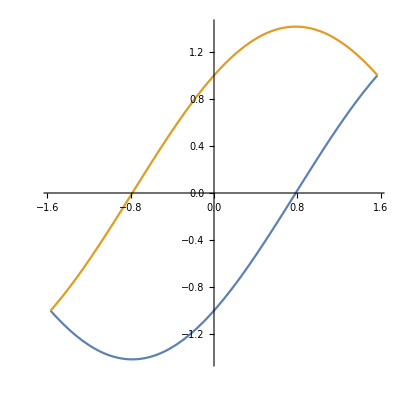

```mathematica
Plot[{Sin[t1]-Cos[t1],Sin[t1]+Cos[t1]},{t1,-Pi/2,Pi/2},AspectRatio->1]
```

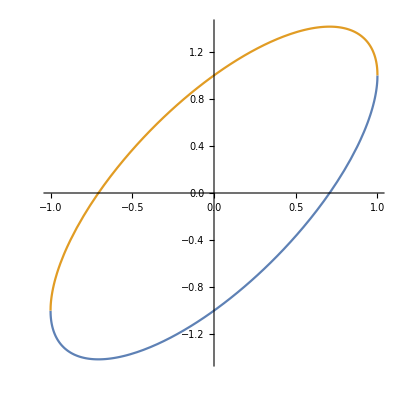

```mathematica
Plot[{x-Sqrt[1-x^2],x+Sqrt[1-x^2]},{x,-1,1},AspectRatio->1]
```

```mathematica
txy[t1_]:={{Cos[t1],Sin[t1],0},{-Sin[t1],Cos[t1],0},{0,0,1}}
```

```mathematica
tyz[t2_]:={{1,0,0},{0,Cos[t2],Sin[t2]},{0,-Sin[t2],Cos[t2]}}
```

```mathematica
tzx[t3_]:={{Cos[t3],0,-Sin[t3]},{0,1,0},{Sin[t3],0,Cos[t3]}}
```

```mathematica
t[t1_,t2_,t3_]:=txy[t1].tyz[t2].tzx[t3]
```

```mathematica
e11:=t[t1,t2,t3][[1]][[1]]
```

```mathematica
e12:=t[t1,t2,t3][[1]][[2]]
```

```mathematica
e11
```

Cos[t1] Cos[t3]+Sin[t1] Sin[t2] Sin[t3]

```mathematica
f11:=x1 x2 x3+Sqrt[1-x1^2]Sqrt[1-x3^2]
```

```mathematica
e12
```

Cos[t2] Sin[t1]

```mathematica
f12:=x1 Sqrt[1-x2^2]
```

```mathematica
e21:=t[t1,t2,t3][[2]][[1]]
```

```mathematica
e22:=t[t1,t2,t3][[2]][[2]]
```

```mathematica
e21
```

-Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3]

```mathematica
f21:=-x1 Sqrt[1-x3^2]+Sqrt[1-x1^2]x2 x3
```

```mathematica
e22
```

Cos[t1] Cos[t2]

```mathematica
f22:=Sqrt[1-x1^2]Sqrt[1-x2^2]
```

```mathematica
e31:=t[t1,t2,t3][[3]][[1]]
```

```mathematica
e32:=t[t1,t2,t3][[3]][[2]]
```

```mathematica
e31
```

Cos[t2] Sin[t3]

```mathematica
f31:=Sqrt[1-x2^2]x3
```

```mathematica
e32
```

-Sin[t2]

```mathematica
f32:=-x2
```

```mathematica
ContourPlot3D[{e11==e21,e21==e31},{t1,-Pi,Pi},{t2,-Pi,Pi},{t3,-Pi,Pi},Mesh->None]
```

-Graphics3D-

```mathematica
ContourPlot3D[{f11==f21},{x1,-1,1},{x2,-1,1},{x3,-1,1},Mesh->None]
```

-Graphics3D-

```mathematica
ContourPlot3D[{f11==f21,f21==f31},{x1,-1,1},{x2,-1,1},{x3,-1,1},Mesh->None]
```

-Graphics3D-

```mathematica
ContourPlot3D[e11+e12==e21+e22,{t1,-Pi,Pi},{t2,-Pi,Pi},{t3,-Pi,Pi},Mesh->None]
```

-Graphics3D-

```mathematica
ContourPlot3D[f11+f12==f21+f22,{x1,-1,1},{x2,-1,1},{x3,-1,1},Mesh->None]
```

-Graphics3D-

```mathematica
ContourPlot3D[{f11+f12==f21+f22,f21+f22==f31+f32},{x1,-1,1},{x2,-1,1},{x3,-1,1},Mesh->None]
```

-Graphics3D-

```mathematica
ContourPlot3D[{f11+f12==f21+f22,f21+f22==f31+f32,f31==0},{x1,-1,1},{x2,-1,1},{x3,-1,1},Mesh->None]
```

-Graphics3D-

```mathematica
result23:=Solve[{f11+f12==f21+f22,f21+f22==f31+f32,f31==0},{x1,x2,x3}]
```

```mathematica
FullSimplify[(f11+f12)/.result23]
```

{√(2/3)}

```mathematica
result13:=Solve[{(f11/.x2->0)==(f21/.x2->0),(f21/.x2->0)==(f31/.x2->0)},{x1,x3}]
```

```mathematica
result13
```

{{x1→-1/(√2),x3→1/(√3)}}

```mathematica
full13:=FullSimplify[f11/.result13/.x2->0]
```

```mathematica
full13
```

{1/(√3)}